```mathematica
randomi1 = RandomInteger[{1,2^2}]
randomi2 = RandomInteger[{1,2^3}]
randomi3 = RandomInteger[{1,2^2}]
randomi4 = RandomInteger[{1,2^3}]
randomk = RandomInteger[{1,2^3}]
```

2

3

3

1

4

```mathematica
AllPathCanyons[g_,j_,i1_,i2_,i3_,i4_,l_,k_]:=Table[
Labeled[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True,
ImageSize->Tiny
],
StringTemplate["{0,left___,left___,s___}->`a`
{1,left___,left___,s___}->`b`
`e`"]
(*{0,1,s___}->`c`
{1,1,s___}->`d`*)
[<|
(*"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]*)
"a"->{s,0,0},
"b"->{s,1,1,0,1},
"e":>Tuples[{0,1},l][[k]]
|>]],
{i,1,Length[VertexList[g]]}
]
```

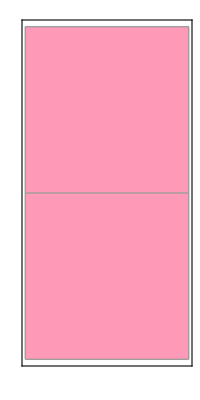
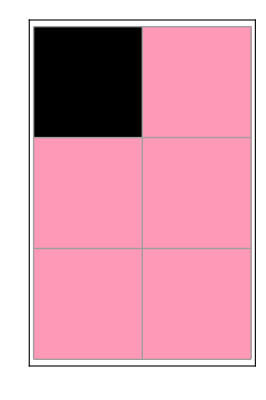
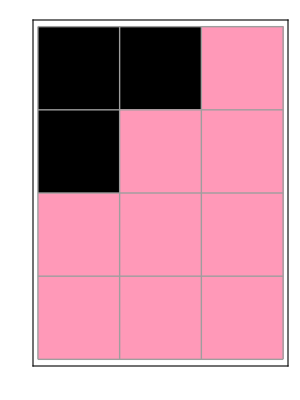
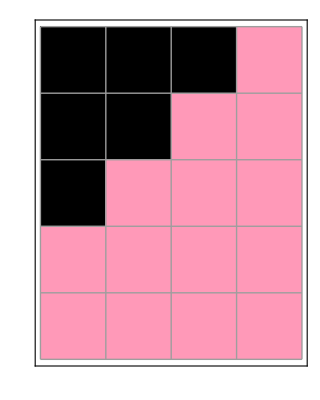
{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0}}

```mathematica
(*A brief repetition of the above.*)
AllPathCanyons[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},2][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)
}],
{Tuples[{0,1},2][[1]]},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
],0,0,0,0,0,2,1]
```

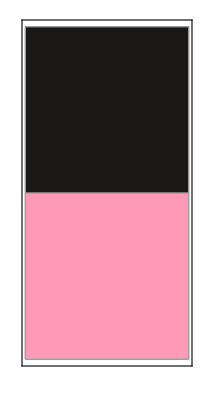
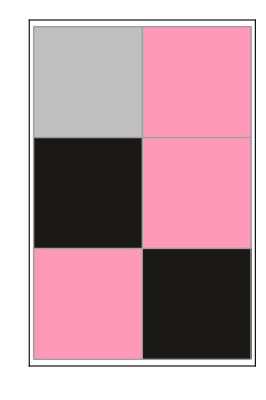
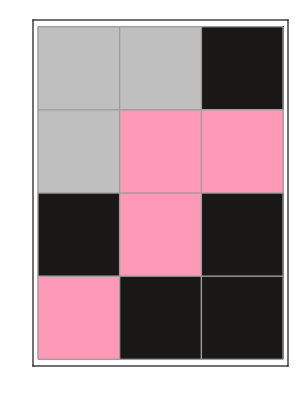
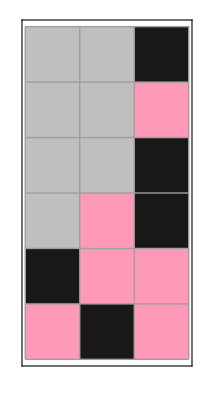
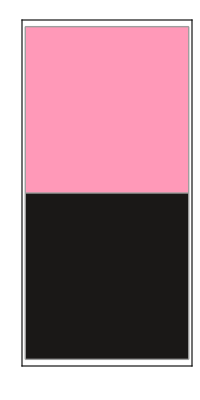
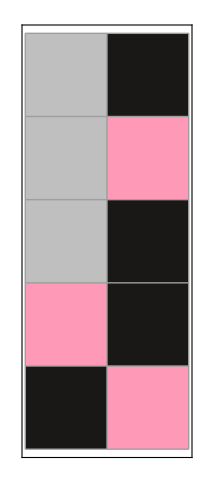
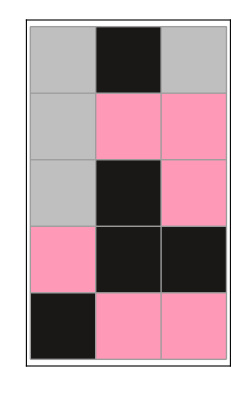
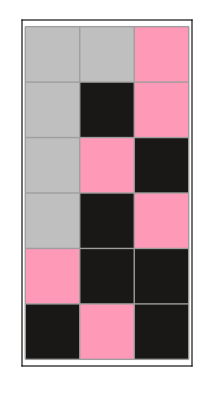
{{{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1}}}}}}}}},{{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0}}}}}}}},{{{{{{{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1}}}}}}}}}}

```mathematica
Table[Table[Table[Table[Table[
AllPathCanyons[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},2][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)
}],
{Tuples[{0,1},l][[k]]},
2,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
],j,i1,i2,i3,i4,l,k],{t,1,1}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,1,2^l}],
{l,2,3}]
```

```mathematica
Length[Flatten[%58,8]]
```

166

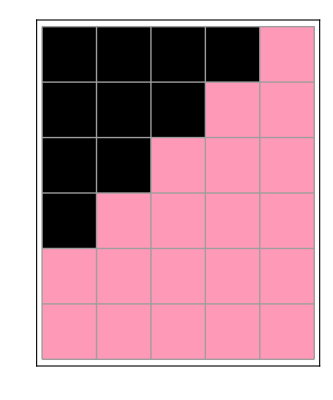
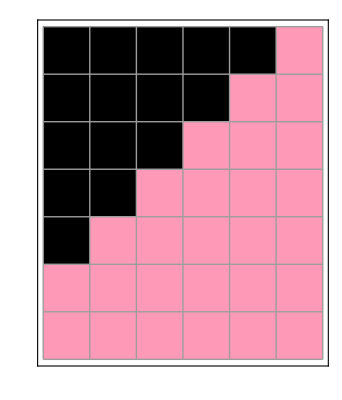
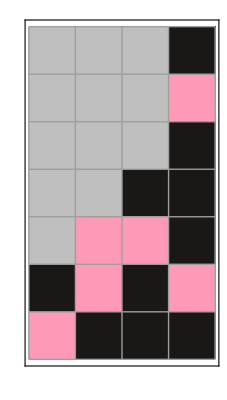
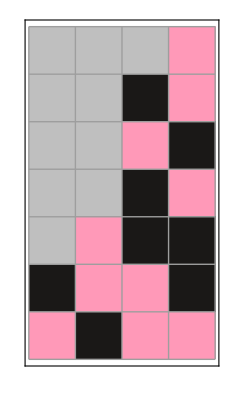
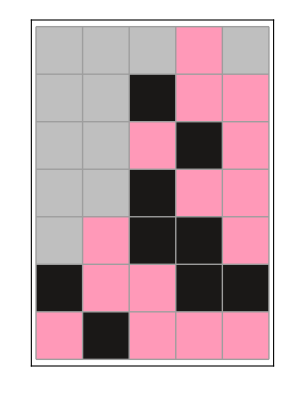
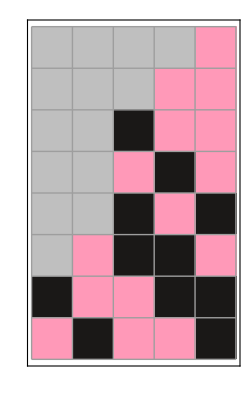
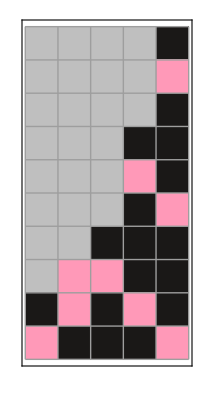
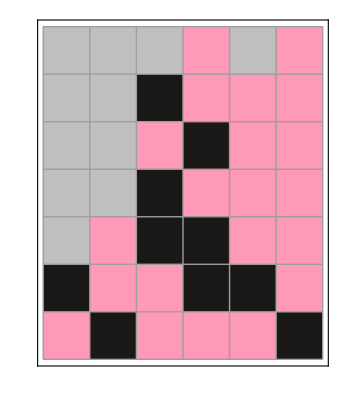
{-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{0, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 0, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 0},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1},-Graphics-{0,left___,left___,s___}->{s, 0, 0}
{1,left___,left___,s___}->{s, 1, 1, 0, 1}
{1, 1, 1}}

```mathematica
PostGenerations = Flatten[%28,8]
```

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,1,0,s___}:>{left,s,1,1,1},
{left___,1,s___}:>{left,s,0,0}
}],
{{0,0,1,0,0,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],{i,1,3}
]
```

{{001001
0000100,001001
0001111,001001
0010000,001001
0000100
00000000,001001
0000100
00000111,001001
0001111
00011100,001001
0000100
00000111
000001100,001001
0001111
00011100
000110000,001001
0001111
00011100
000110111,001001
0000100
00000111
000001100
0000010000,001001
0000100
00000111
000001100
0000010111,001001
0001111
00011100
000110000
0001000000,001001
0001111
00011100
000110000
0001000111,001001
0001111
00011100
000110111
0001011100,001001
0001111
00011100
000110111
0001101100,001001
0001111
00011100
000110111
0001111111,001001
0000100
00000111
000001100
0000010000
00000000000,001001
0000100
00000111
000001100
0000010000
00000000111,001001
0000100
00000111
000001100
0000010111
00000011100,001001
0000100
00000111
000001100
0000010111
00000101100,001001
0000100
00000111
000001100
0000010111
00000111111,001001
0001111
00011100
000110000
0001000111
00010001100,001001
0001111
00011100
000110111
0001011100
00001110000,001001
0001111
00011100
000110111
0001011100
00010110000,001001
0001111
00011100
000110111
0001011100
00010110111,001001
0001111
00011100
000110111
0001011100
00011100111,001001
0001111
00011100
000110111
0001101100
00011010000,001001
0001111
00011100
000110111
0001101100
00011010111,001001
0001111
00011100
000110111
0001111111
00011111100},{001001
0000100,001001
0001111,001001
0010000,001001
0000100
00000000,001001
0000100
00000111,001001
0001111
00011100,001001
0000100
00000111
000001100,001001
0001111
00011100
000110000,001001
0001111
00011100
000110111,001001
0000100
00000111
000001100
0000010000,001001
0000100
00000111
000001100
0000010111,001001
0001111
00011100
000110000
0001000000,001001
0001111
00011100
000110000
0001000111,001001
0001111
00011100
000110111
0001011100,001001
0001111
00011100
000110111
0001101100,001001
0001111
00011100
000110111
0001111111,001001
0000100
00000111
000001100
0000010000
00000000000,001001
0000100
00000111
000001100
0000010000
00000000111,001001
0000100
00000111
000001100
0000010111
00000011100,001001
0000100
00000111
000001100
0000010111
00000101100,001001
0000100
00000111
000001100
0000010111
00000111111,001001
0001111
00011100
000110000
0001000111
00010001100,001001
0001111
00011100
000110111
0001011100
00001110000,001001
0001111
00011100
000110111
0001011100
00010110000,001001
0001111
00011100
000110111
0001011100
00010110111,001001
0001111
00011100
000110111
0001011100
00011100111,001001
0001111
00011100
000110111
0001101100
00011010000,001001
0001111
00011100
000110111
0001101100
00011010111,001001
0001111
00011100
000110111
0001111111
00011111100},{001001
0000100,001001
0001111,001001
0010000,001001
0000100
00000000,001001
0000100
00000111,001001
0001111
00011100,001001
0000100
00000111
000001100,001001
0001111
00011100
000110000,001001
0001111
00011100
000110111,001001
0000100
00000111
000001100
0000010000,001001
0000100
00000111
000001100
0000010111,001001
0001111
00011100
000110000
0001000000,001001
0001111
00011100
000110000
0001000111,001001
0001111
00011100
000110111
0001011100,001001
0001111
00011100
000110111
0001101100,001001
0001111
00011100
000110111
0001111111,001001
0000100
00000111
000001100
0000010000
00000000000,001001
0000100
00000111
000001100
0000010000
00000000111,001001
0000100
00000111
000001100
0000010111
00000011100,001001
0000100
00000111
000001100
0000010111
00000101100,001001
0000100
00000111
000001100
0000010111
00000111111,001001
0001111
00011100
000110000
0001000111
00010001100,001001
0001111
00011100
000110111
0001011100
00001110000,001001
0001111
00011100
000110111
0001011100
00010110000,001001
0001111
00011100
000110111
0001011100
00010110111,001001
0001111
00011100
000110111
0001011100
00011100111,001001
0001111
00011100
000110111
0001101100
00011010000,001001
0001111
00011100
000110111
0001101100
00011010111,001001
0001111
00011100
000110111
0001111111
00011111100}}

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
randomi2
```

4

```mathematica
Tuples[{0,1},3][[randomi1]]
```

{0,1,0}

```mathematica
Tuples[{0,1},3][[randomi2]]
```

{0,1,1}

```mathematica
Tuples[{0,1},3][[randomi3]]
```

Part::pkspec1: The expression $Failed cannot be used as a part specification.

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}⟦$Failed⟧

```mathematica
Tuples[{0,1},3][[randomi4]]
```

{0,0,1}

```mathematica
Tuples[{0,1},3][[randomk]]
```

{0,0,0}

```mathematica
AllPathCanyons[g_]:=Table[
(*Labeled[*)
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True,
ImageSize->Tiny
]
,StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0,1},
"b"->{0,1,1},
"c":>{0,1,1},
"d":>{0,1,1},
"e":>{0,1,0}
|>]
],
{i,1,Length[VertexList[g]]}
]

AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,0},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}